```mathematica
SetDirectory[NotebookDirectory[]]
lightconeGenericModel = "./LightCone";
shockwaveModel = "./Shockwave";
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

SetDelayed::wrsym: Symbol Discard is Protected.

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## FeynCalc Setup:

```mathematica
$FCDefaultLightconeVectorN=Sqrt[2]n1;
$FCDefaultLightconeVectorNB=Sqrt[2]n2;
FCClearScalarProducts[];
SP[Sqrt[2]n1,Sqrt[2]n1]=0;//FCI;
SP[Sqrt[2]n2,Sqrt[2]n2]=0;//FCI;
SP[Sqrt[2]n1,n1]=0;//FCI;
SP[Sqrt[2]n2,n2]=0;//FCI;
SP[n1,n1]=0//FCI;
SP[n2,n2]=0//FCI;
SP[n1,n2] = 1 //FCI;
SP[Sqrt[2]n2,n1] = Sqrt[2]//FCI;
SP[Sqrt[2]n1,n2] = Sqrt[2]//FCI;
(*Need to multiply and divide by Sqrt[2] to not broke feyncalc*)
plus[x_]:=SP[Sqrt[2]n2,x]/Sqrt[2];
minus[x_]:=(SP[x]-SPLR[x])/(2 plus[x])
d = D-2;
Gplus = FCI[GS[Sqrt[2]n2]]/Sqrt[2];
Gminus = FCI[GS[Sqrt[2]n1]]/Sqrt[2];

(*Allow to compute correctly the factor Sqrt[2] /!\ apply it at the end!!!*)
SimplifySqrt2:={Momentum[Sqrt[2]*n1,4]->Sqrt[2]*Momentum[n1,4],Momentum[Sqrt[2]*n2,4]->Sqrt[2]*Momentum[n2,4],SP[Sqrt[2] n2,x_]->Sqrt[2]SP[n2,x]}
NiceNotation:={FCI[SP[n1,a_]]:>Superscript[a,"-"],FCI[SP[n2,b_]]:>Superscript[b,"+"],DiracGamma[Momentum[n2,4],4]->Superscript[γ,"+"],DiracGamma[Momentum[n1,4],4]->Superscript[γ,"-"],
FCI[Polarization[k_,___]]:>ϵ[k],
Pair[LightConePerpendicularComponent[Momentum[a__],√2 Momentum[n1],√2 Momentum[n2]],LightConePerpendicularComponent[Momentum[b__],√2 Momentum[n1],√2 Momentum[n2]]]:>Subscript[(OverBar[a].OverBar[b]),"⊥"]
};
```

## Generate Shockwave:

```mathematica
CountExternalParticle[topology_]:=Length[Cases[topology,Propagator[ty_][___]/;ty===Outgoing]];GenerateShockwave[t_]:=Module[{targetVertex,amputedTop,top,listVertexs,x,y},top=t;
(*Return the list of possible positions of the shockwave.*)
listVertexs={};
(*Execute while there is internal propagator in the topology*)
While[Length[Vertices[top]]>1,(*Collect external propagators*)
AppendTo[listVertexs,DeleteCases[top/.{Topology[_][x__]->{x}}/.{Propagator[Outgoing][x__]->{x}},Propagator[__][___],{1}]];
(*choose the vertex that is common to two outgoing propagators*)
targetVertex=DeleteCases[Tally[Flatten[Cases[top,Propagator[Outgoing][__]]/.{Propagator[__][x__,y__]->{x,y}}]],{_,n_}/;n<2][[1]][[1]];
amputedTop=DeleteCases[top,Propagator[Outgoing][x__,y__]/;x==targetVertex||y==targetVertex]/. {Propagator[Internal][targetVertex,x_]->Propagator[Outgoing][targetVertex,x],Propagator[Internal][x_,targetVertex]->Propagator[Outgoing][x,targetVertex]};
top=amputedTop;];
 AppendTo[listVertexs,DeleteCases[top/.{Topology[_][x__]->{x}}/.{Propagator[Outgoing][x__]->{x}},Propagator[__][___],{1}]];
DeleteCases[listVertexs,{}]]

NewTopology[top_,shockwaveList_]:=
Module[{amputedList,outgoingList,incomingList,internalList,list,numberShockwave,shockwaveVerticesIndices,maxExternalIndice,newVertex,newVertexList,maxVertexIndice},list=top/.Topology[1]->List;
(*Create a new topology with the additionnal external leg for a given shockwave position (ie. the ntuple of intercepted propagators)*)
numberShockwave=Length[shockwaveList];
shockwaveVerticesIndices=shockwaveList/.{Vertex[n1_][n2_],Vertex[n3_][n4_]}->{n1,n2,n3,n4};
maxExternalIndice=Min[Vertices[top]/.Vertex[_][n_]->n]-1;
maxVertexIndice=Max[Vertices[top]/.Vertex[_][n_]->n];
amputedList=DeleteCases[list,Propagator[__][x__,y__]/;MemberQ[shockwaveList,{x,y}]];
outgoingList=Cases[amputedList,Propagator[Outgoing][___]]/.Propagator[Outgoing][Vertex[1][m_],Vertex[n_][l_]]->Propagator[Outgoing][Vertex[1][m],Vertex[n][l+numberShockwave]];
incomingList=Cases[amputedList,Propagator[Incoming][___]]/.Propagator[Incoming][Vertex[1][1],Vertex[m_][n_]]->Propagator[Incoming][Vertex[1][1],Vertex[m][n+numberShockwave]];
internalList=Cases[amputedList,Propagator[Internal][___]]/.{Vertex[m_][n_]->Vertex[m][n+numberShockwave]};
newVertex[i_]:=If[shockwaveVerticesIndices[[i]][[1]]==1,{Propagator[Outgoing][Vertex[1][shockwaveVerticesIndices[[i]][[2]]],Vertex[3][maxVertexIndice+numberShockwave+i]],Propagator[Internal][Vertex[shockwaveVerticesIndices[[i]][[3]]][shockwaveVerticesIndices[[i]][[4]]+numberShockwave],Vertex[3][maxVertexIndice+numberShockwave+i]],Propagator[Outgoing][Vertex[1][maxExternalIndice+i],Vertex[3][maxVertexIndice+numberShockwave+i]]},{Propagator[Internal][Vertex[3][shockwaveVerticesIndices[[i]][[2]]+numberShockwave],Vertex[3][maxVertexIndice+numberShockwave+i]],Propagator[Internal][Vertex[shockwaveVerticesIndices[[i]][[3]]][maxVertexIndice+numberShockwave+i],Vertex[3][shockwaveVerticesIndices[[i]][[4]]+numberShockwave]],Propagator[Outgoing][Vertex[1][maxExternalIndice+i],Vertex[3][maxVertexIndice+numberShockwave+i]]}];
newVertexList=Flatten[Map[newVertex,Range[1,numberShockwave]]];
Topology[1][Join[incomingList,outgoingList,Cases[newVertexList,Propagator[Outgoing][___]],internalList,Cases[newVertexList,Propagator[Internal][___]]]/.List->Sequence]]

NewTopologyList[topology_]:=Module[{shockwaveList},
(*for given topology, give all possible topologies with shockwave*)
shockwaveList=GenerateShockwave[topology];
TopologyList[Map[NewTopology[topology,#]&,shockwaveList]/.List->Sequence]]

CountExternalParticle[topology_]:=Length[Cases[topology,Propagator[x_][___]/;x===Outgoing]]
```

## Energy denominator:

```mathematica
IntermediateStates[inputDiagram_]:=
(*For a given diagramm, compute all intermediate states (in the sense of LC perturbation theory)*)
Module[{shockwaveFields,interactingShockwaveFields,allTheStuff,allPropagators,initialState,listOfState,currentState,InteractWithShockwaveQ,nextStateBeforeSh,nextStateAfterSh,diagram,x,y,z,f,l,p,state,propag,listPropagator},
If[Head[Head[inputDiagram]]===TopologyList,diagram=inputDiagram[[1]],diagram=inputDiagram];
allTheStuff = Level[diagram,{-3}];
allPropagators = Cases[allTheStuff,Propagator[__][___]];
shockwaveFields=DeleteDuplicates[DeleteCases[allTheStuff,Except[Field[_]->S[4]]]]/.(Field[x_]->S[4]):>Field[x];
interactingShockwaveFields = Cases[FieldPoints[diagram[[1]]],FieldPoint[0][x__,y__,z__]/;MemberQ[shockwaveFields,x]||MemberQ[shockwaveFields,y]||MemberQ[shockwaveFields,z]]/.AntiParticle[f__]->f/.FieldPoint[0][l___]->Sequence[l];
InteractWithShockwaveQ [propag_]:=MemberQ[interactingShockwaveFields,propag/.Propagator[__][___,Field[x_]]->Field[x]];

NextStateBeforeSh[state_,listPropagator__] := If[state[[-1]],
state,
Cases[listPropagator,
Propagator[Internal][state[[2]][[2]],___]|Propagator[Internal][__,state[[2]][[2]],__]|Propagator[Internal][state[[2]][[1]],___]|Propagator[Internal][__,state[[2]][[1]],__]]
/.p:Propagator[__][___]:>{"Before",p,InteractWithShockwaveQ[p]}];

NextStateAfterSh[state_,listPropagator__] := If[state[[-1]],
state,
Cases[listPropagator,
Propagator[Internal][state[[2]][[2]],___]|Propagator[Internal][__,state[[2]][[2]],__]|Propagator[Internal][state[[2]][[1]],___]|Propagator[Internal][__,state[[2]][[1]],__]|Propagator[Outgoing][___,state[[2]][[2]],___]]
/.p:Propagator[__][___]:>{"After",p,MatchQ[p,Propagator[Outgoing][___]]}];

UpdatePropagatorList[statelist_,listPropagator__]:=DeleteCases[listPropagator,p:Propagator[__][___]/;MemberQ[statelist[[All,2]],p]];


initialState = {{"Before",Cases[allTheStuff,Propagator[Incoming][___]][[1]],False}};
listOfState = {initialState};
currentState = initialState;
allPropagators=UpdatePropagatorList[currentState,allPropagators];
While[Not[And@@currentState[[All,-1]]],
currentState = Level[Map[NextStateBeforeSh[#,allPropagators]&,currentState],{-4}];
allPropagators=UpdatePropagatorList[currentState,allPropagators];
AppendTo[listOfState,currentState];
];
listOfState[[-1,All,-1]]=False;
currentState = listOfState[[-1]];
allPropagators=UpdatePropagatorList[currentState,allPropagators];
While[Not[And@@currentState[[All,-1]]],
currentState = Level[Map[NextStateAfterSh[#,allPropagators]&,currentState],{-4}];
allPropagators=UpdatePropagatorList[currentState,allPropagators];
AppendTo[listOfState,currentState];
];
listOfState = DeleteCases[listOfState,{__,Propagator[__][___,f:Field[__]],__}/;MemberQ[shockwaveFields,f],{-4}];
listOfState[[2;;-2,All,1;;2]]
];

SingleEnergyDenominator[state_,incomingList_,outgoingList_,momentum_]:=Module[{intermediateMomentum,denom,type,outgoigMomentum,incomingMomentum},
(*Compute the energy denominator related to a intermediate state*)
outgoigMomentum = FourMomentum[Outgoing,#]&/@outgoingList;
incomingMomentum = FourMomentum[Incoming,#]&/@incomingList;
intermediateMomentum = state[[All,-1]]/.Propagator[type__][___,Field[x_]]:>minus[FourMomentum[type,momentum[x]]];
If[state[[1,1]]==="Before",
denom = - ⅈ (minus[Plus@@incomingMomentum]-Plus@@intermediateMomentum),
denom = ⅈ(minus[Plus@@outgoigMomentum]-Plus@@intermediateMomentum)];
1/denom
];

EnergyDenominator[diagram_,momentum_]:=Module[{states,denominators,incomingList,outgoingList,allTheStuff},
(*Compute the product of energy denominators of a given diagram*)
allTheStuff = Level[diagram, {-3}];
incomingList  = Cases[allTheStuff,Propagator[Incoming][___,Field[x_]]:>momentum[x]];
outgoingList = Cases[allTheStuff,Propagator[Outgoing][___,Field[x_]]:>momentum[x]];
states = IntermediateStates[diagram];
denominators = Map[ SingleEnergyDenominator[#,incomingList,outgoingList,momentum]&,states];
Times@@denominators
];

WrapperSingleEnergyDenominator[nField_,diagram_,momentum_]:=Module[{states,s,incomingList,outgoingList,allTheStuff},
(*Wrapper used in the instantaneous contribution*)
allTheStuff = Level[diagram, {-3}];
incomingList  = Cases[allTheStuff,Propagator[Incoming][___,Field[x_]]:>momentum[x]];
outgoingList = Cases[allTheStuff,Propagator[Outgoing][___,Field[x_]]:>momentum[x]];
states =  Cases[IntermediateStates[diagram],s:{___}/;MemberQ[s,{___,Propagator[_][___,Field[nField]]}]];
If[Length[states]===1,SingleEnergyDenominator[states[[1]],incomingList,outgoingList,momentum],Message[WrapperSingleEnergyDenominator::len,nField,states];0]];
WrapperSingleEnergyDenominator::len="Field[`1`] appears in 0 or more than 1 intermediate state:`2`";
```

## Momentum Conservation:

```mathematica
MomentumReplacementRules[inputDiagram__,momentum_]:=
(*Give the replacement rules to apply to apply momentum conservation rules*)
Module[{nFieldtoPropagatorType,propagators,priority,internalPropagators,fieldPoints,DecideReplacement,replacementRules,diagram,x,l,y},
If[Head[Head[inputDiagram]]===TopologyList,diagram=inputDiagram[[1]],diagram=inputDiagram];
propagators = Cases[Level[diagram,{-3}],Propagator[__][___]];
nFieldtoPropagatorType = Association[ propagators/.Propagator[type_][___,Field[x_]]:>x->type];
priority = propagators/.{Propagator[Incoming][___]->2,Propagator[Outgoing][___]->-1,Propagator[Internal][___]->0};
internalPropagators = Reverse[Cases[propagators,Propagator[Internal][___,Field[x_],___]:>x]];
fieldPoints = FieldPoints[diagram[[1]]];
DecideReplacement[replacementList_,nField_]:=Module[{possibleReplacement,replacementRule},
possibleReplacement = Cases[fieldPoints,l:FieldPoint[_][___]/;MemberQ[Level[l,{-2}],Field[nField]]:>DeleteCases[Level[l,{-2}],Field[nField]]];
replacementRule = Field[nField]->Plus@@SortBy[possibleReplacement,#/.{Field[x_],Field[y_]}:>priority[[x]]+priority[[y]]&][[1]];
priority[[nField]]=replacementRule[[2]]/.__[x_]:>priority[[x]];
Append[replacementList,replacementRule]
];
replacementRules = Fold[DecideReplacement,{},internalPropagators];
replacementRules/.Field[x_]:>FourMomentum[nFieldtoPropagatorType[x],momentum[x]]
];

ReindexMomentum[inputDiagram_,momentum_]:=Module[{f,diagram,incomingList,outgoingList,allTheStuff,l1,l2},
If[Head[Head[inputDiagram]]===TopologyList,diagram=inputDiagram[[1]],diagram=inputDiagram];
allTheStuff = Level[diagram, {-3}];
incomingList  = Cases[allTheStuff,Propagator[Incoming][___,Field[x_]]:>momentum[x]];
outgoingList = Cases[allTheStuff,Propagator[Outgoing][___,Field[x_]]:>momentum[x]];
f[momentum[x_],l_]:=x->l[[1]];
l2 = MapIndexed[f,outgoingList];
l1 = MapIndexed[f,incomingList];
 momentum -> Association[Append[l1,l2]]
];
```

## Instantaneous Contribution

```mathematica
PropagatorReplacementRules[diagram_,momentum_]:=Module[{allTheStuff,shockwaveFields,interactingShockwaveFields,propagatorReplacementRules,incomingList,outgoingList,x,y,z,f,l,ty,li1,li2,mom},
allTheStuff = Level[diagram, {-3}];
incomingList  = Cases[allTheStuff,Propagator[Incoming][___,Field[x_]]:>momentum[x]];
outgoingList = Cases[allTheStuff,Propagator[Outgoing][___,Field[x_]]:>momentum[x]];
shockwaveFields=DeleteDuplicates[DeleteCases[allTheStuff,Except[Field[_]->S[4]]]]/.(Field[x_]->S[4]):>Field[x];
interactingShockwaveFields = Cases[FieldPoints[diagram[[1]][[1]]],FieldPoint[0][x__,y__,z__]/;MemberQ[shockwaveFields,x]||MemberQ[shockwaveFields,y]||MemberQ[shockwaveFields,z]]//.{AntiParticle[f__]->f,FieldPoint[0][l___]->Sequence[l],Field[x_]->x};
propagatorReplacementRules = {FermionNumeratorPropagator[-FourMomentum[ty_,mom:momentum[x_]]]:>If[FreeQ[interactingShockwaveFields,x],-  FADiracSlash[FourMomentum[ty,mom]]+ⅈ Gplus/WrapperSingleEnergyDenominator[x,diagram,momentum],-FADiracSlash[FourMomentum[ty,mom]]],
FermionNumeratorPropagator[FourMomentum[ty_,mom:momentum[x_]]]:>If[FreeQ[interactingShockwaveFields,x],  FADiracSlash[FourMomentum[ty,mom]]-ⅈ Gplus/WrapperSingleEnergyDenominator[x,diagram,momentum], FADiracSlash[FourMomentum[ty,mom]]],
VectorNumeratorPropagator[FourMomentum[ty_,mom:momentum[x_]],li1_,li2_]:>If[FreeQ[interactingShockwaveFields,x],
FAMetricTensor[li1,li2]-(FAFourVector[Sqrt[2]n2,li1]*FAFourVector[FourMomentum[ty,mom],li2]+FAFourVector[Sqrt[2]n2,li2]*FAFourVector[FourMomentum[ty,mom],li1])/(2 plus[FourMomentum[ty,mom]]),
FAMetricTensor[li1,li2]*plus[FourMomentum[ty,mom]]
]}
]
```

## gamma -> qqbar gamma:

Start here:

```mathematica
InitializeModel[shockwaveModel,GenericModel->lightconeGenericModel];
```

/home/nicolas/Documents/StageM2_2024_2025/shockwaveAutomation

loading generic model file /home/nicolas/Documents/StageM2_2024_2025/shockwaveAutomation/LightCone.gen

> $GenericMixing is OFF

generic model {./LightCone} initialized

loading classes model file /home/nicolas/Documents/StageM2_2024_2025/shockwaveAutomation/Shockwave.mod

loading classes model file /home/nicolas/.Wolfram/Applications/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 50 particles (incl. antiparticles) in 19 classes

> $CounterTerms are ON

> 97 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {./Shockwave} initialized

### Topologies:

> Top. 1 ae/becfdf/ef.m, 0 diagrams

> Top. 2 ae/bfcedf/ef.m, 0 diagrams

> Top. 3 ae/bfcfde/ef.m, 0 diagrams

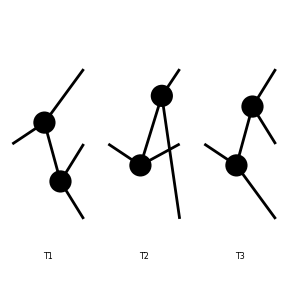

```mathematica
initialTopology = CreateTopologies[0,1->3,Adjacencies->{3}];
Paint[initialTopology];
```

> Top. 1 ah/bjejckfkdlgl/hihjikil.m, 0 diagrams

> Top. 2 ag/chdhbieifj/gigjjh.m, 0 diagrams

> Top. 3 ah/bjejckfkdlgl/hiijhkil.m, 0 diagrams

> Top. 4 ag/bhdhcieifj/gigjjh.m, 0 diagrams

> Top. 5 ah/bjejckfkdlgl/hiijikhl.m, 0 diagrams

> Top. 6 ag/bhchdieifj/gigjjh.m, 0 diagrams

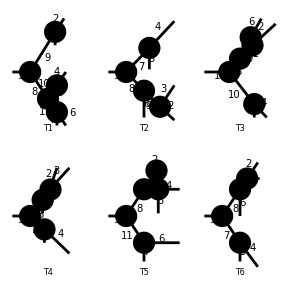

```mathematica
shockwaveTopology = Map[NewTopologyList,initialTopology];
Paint[shockwaveTopology,FieldNumbers->True];
```

Excluding 0 Generic, 7 Classes, and 7 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

Restoring 0 Generic, 7 Classes, and 7 Particles fields

in total: 2 Classes insertions

> Top. 1 ah/bjejckfkdlgl/hiijhkil.m, 0 diagrams

> Top. 2 ah/bjejckfkdlgl/hiijikhl.m, 0 diagrams

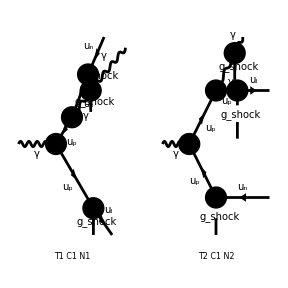

```mathematica
shockwaveTopology = DiagramDelete[shockwaveTopology,{2,4,6}];
diags = InsertFields[shockwaveTopology,V[1]->{V[1],S[4],F[3],S[4],-F[3],S[4]},ExcludeParticles->{S[_],V[x_]/;1<x<5},GenericModel->lightconeGenericModel,Model->{shockwaveModel},InsertionLevel->{Classes}];
Paint[diags,PaintLevel->InsertionLevel];
```

### Kinematics:

```mathematica
FCClearScalarProducts[];
SP[Sqrt[2]n1,Sqrt[2]n1]=0//FCI;
SP[Sqrt[2]n2,Sqrt[2]n2]=0//FCI;
SP[Sqrt[2]n1,n1]=0//FCI;
SP[Sqrt[2]n2,n2]=0//FCI;
SP[n1,n1]=0//FCI;
SP[n2,n2]=0//FCI;
SP[n1,n2] = 1 //FCI;
SP[Sqrt[2]n2,n1] = Sqrt[2]//FCI;
SP[Sqrt[2]n1,n2] = Sqrt[2]//FCI;
SP[Sqrt[2]n1,Sqrt[2]n2]=2//FCI;
SP[Sqrt[2]n2,Subscript[p, 1]]=0//FCI;
SP[Sqrt[2]n2,Subscript[p, 2]]=0//FCI;
SP[Sqrt[2]n2,Subscript[p, q]] = Subscript[x, q] SP[Sqrt[2]n2,Subscript[p, "γ"]]//FCI;
SP[Sqrt[2]n2,Subscript[p, OverBar[q]]] = Subscript[x, OverBar[q]] SP[Sqrt[2]n2,Subscript[p, "γ"]]//FCI;
SP[Sqrt[2]n2, k] = Subscript[x, k] SP[Sqrt[2]n2,Subscript[p, "γ"]]//FCI;
 Pair[Momentum[√2 n2],Momentum[Polarization[k,-ⅈ,Transversality->True]]]=0//FCI;
Pair[Momentum[√2 n1],Momentum[Polarization[k,-ⅈ,Transversality->True]]] =-Sqrt[2]Pair[LightConePerpendicularComponent[Momentum[k],Momentum[√2 n1],Momentum[√2 n2]],LightConePerpendicularComponent[Momentum[Polarization[k,-ⅈ,Transversality->True]],Momentum[√2 n1],Momentum[√2 n2]]]/plus[k] //FCI;

SP[Subscript[p, "γ"],Subscript[p, "γ"]]=-Q^2//FCI;
SPLR[-Subscript[p, 2]+Subscript[p, OverBar[q]]+k ,-Subscript[p, 2]+Subscript[p, OverBar[q]]+k ,√2 n1,√2 n2] = SPLR[-Subscript[p, 1]+Subscript[p, q],-Subscript[p, 1]+Subscript[p, q],√2 n1,√2 n2]//FCI;
SPLR[Subscript[p, "γ"],Subscript[p, "γ"],√2 n1,√2 n2]=0//FCI;
SP[Subscript[p, OverBar[q]]-Subscript[p, 2],Subscript[p, OverBar[q]]-Subscript[p, 2]] = 0//FCI;
SP[Subscript[p, OverBar[q]]-Subscript[p, 2]+k,Subscript[p, OverBar[q]]-Subscript[p, 2]+k] = 0//FCI;
SP[Subscript[p, q]-Subscript[p, 1],Subscript[p, q]-Subscript[p, 1]]=0//FCI;
SP[k,k] = 0//FCI;
$Assumptions=Subscript[x, q] + Subscript[x, k]+Subscript[x, OverBar[q]]==1&&Subscript[x, k]∈PositiveReals&&Subscript[x, OverBar[q]]∈PositiveReals&&Subscript[x, q]∈PositiveReals&&Pair[Momentum[n2],Momentum[Subscript[p, "γ"]]]∈PositiveReals&&SP[Sqrt[2]n2,Subscript[p, "γ"]]∈PositiveReals;
```

### Photon before shockwave:

> Top. 1 ah/bjejckfkdlgl/hiijhkil.m, 0 diagrams

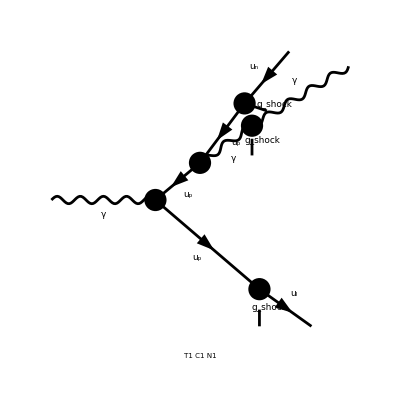

```mathematica
diagBeforeShockwave = DiagramExtract[diags,1];
Paint[diagBeforeShockwave,ImageSize->{512,256}];
propagatorReplacementRules = PropagatorReplacementRules[diagBeforeShockwave,momentum];
energyDenominator = EnergyDenominator[diagBeforeShockwave,momentum];
mRR = MomentumReplacementRules[diagBeforeShockwave,momentum];
reIndex = ReindexMomentum[diagBeforeShockwave,momentum];
```

```mathematica
diagWithMomentum = diagBeforeShockwave/.Propagator[ty__][vertex___,Field[x_]]->Propagator[ty][vertex,Field[x],momentum[x]];
ePPhoton= Conjugate[PolarizationVector[k,LorentzIndex[Lor2],Transversality->True]];
amp =CreateFeynAmp[diagWithMomentum,AmplitudeLevel->{Classes},MomentumConservation->False,Truncated->True,PreFactor->(2π)^3];
amp[[1,3]] = CreateFeynAmp[diagWithMomentum,AmplitudeLevel->{Classes},MomentumConservation->False,Truncated->True,PreFactor->(2π)^3][[1,3]]EnergyDenominator[diagBeforeShockwave,momentum]//.propagatorReplacementRules//.mRR/.reIndex;
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

```mathematica
ampConverted = Contract[Simplify[DiracSubstitute67[FCFAConvert[amp,IncomingMomenta->{Subscript[p, "γ"]},OutgoingMomenta->{k,0,Subscript[p, q],-Subscript[p, 1],Subscript[p, OverBar[q]],-Subscript[p, 2]},DropSumOver->True,SMP->True][[1]]]SUNFDelta[SUNFIndex[Col4],SUNFIndex[Col6]] /Sqrt[SUNN]ePPhoton]]/.SMP["e"]->3/2 SMP["e_Q"]SMP["e"]
```

-(((γ̄·OverBar[√2 n2]).(γ̄·((p̄)_q-(p̄)_1)).(γ̄)^Lor1.(2 γ̄·(k̄-(p̄)_2+(p̄)_(q̄))+γ̄·OverBar[√2 n2] (Q^2/(OverBar[√2 n2]·(p̄)_γ)-(((((p̄)_1)^2)_⊥-2 (((p̄)_1·(p̄)_q)_⊥)+(((p̄)_q)^2)_⊥) ((OverBar[√2 n2]·(p̄)_γ) x_k+(OverBar[√2 n2]·(p̄)_γ) x_q+(OverBar[√2 n2]·(p̄)_γ) x_(q̄)))/((OverBar[√2 n2]·(p̄)_γ) x_q ((OverBar[√2 n2]·(p̄)_γ) x_k+(OverBar[√2 n2]·(p̄)_γ) x_(q̄))))).(γ̄·(ε̄)^*(k)).(γ̄·((p̄)_(q̄)-(p̄)_2)).(γ̄·OverBar[√2 n2]) FWilsonLine(Col6,Col8,-p_2) FWilsonLine(Col8,Col4,-p_1) (OverBar[√2 n2]·(p̄)_γ)/(√2) ((OverBar[√2 n2]·(p̄)_γ) x_k)/(√2) ((OverBar[√2 n2]·(p̄)_γ) x_q)/(√2) ((OverBar[√2 n2]·(p̄)_γ) x_(q̄))/(√2) IndexDelta(Gen4,Gen8) IndexDelta(Gen6,Gen8) (OverBar[√2 n2]·(p̄)_γ)^(5/2) e^2 e_Q^2 x_q (x_q+x_(q̄)-1) δ_Col4Col6)/(32 √2 π √N √((OverBar[√2 n2]·(p̄)_γ) x_k) √((OverBar[√2 n2]·(p̄)_γ) x_q) √((OverBar[√2 n2]·(p̄)_γ) x_(q̄)) (((((p̄)_1)^2)_⊥-2 (((p̄)_1·(p̄)_q)_⊥)+(((p̄)_q)^2)_⊥) (OverBar[√2 n2]·(p̄)_γ) ((OverBar[√2 n2]·(p̄)_γ) x_k+(OverBar[√2 n2]·(p̄)_γ) x_q+(OverBar[√2 n2]·(p̄)_γ) x_(q̄))-Q^2 (OverBar[√2 n2]·(p̄)_γ) x_q ((OverBar[√2 n2]·(p̄)_γ) x_k+(OverBar[√2 n2]·(p̄)_γ) x_(q̄))) (0_⊥ x_q x_(q̄) (OverBar[√2 n2]·(p̄)_γ)^2+x_k (((((p̄)_2)^2)_⊥-2 (((p̄)_2·(p̄)_(q̄))_⊥)+(((p̄)_(q̄))^2)_⊥) x_q (OverBar[√2 n2]·(p̄)_γ)^2+(((((p̄)_1)^2)_⊥-2 (((p̄)_1·(p̄)_q)_⊥)+(((p̄)_q)^2)_⊥) (OverBar[√2 n2]·(p̄)_γ)-Q^2 (OverBar[√2 n2]·(p̄)_γ) x_q) x_(q̄) (OverBar[√2 n2]·(p̄)_γ)))))

#### + component:

```mathematica
ampConverted/.DiracGamma[LorentzIndex[Lor1,4],4]->Gplus;
%//Simplify;
%//ToLightConeComponents;
%//DiracSimplify;
%//Simplify;
SUNSimplify[%/.SimplifySqrt2//Simplify,SUNNToCACF->False];
plusComponent = %/.FWilsonLine[col1_,col2_,-mom1_]FWilsonLine[col2_,col1_,-mom2_]->-SUNN*U[mom1,mom2]/.SMP["e"]->3/2 SMP["e_Q"]SMP["e"]//Simplify
%//.NiceNotation
```

#### perp component:

```mathematica
ampConverted/.DiracGamma[LorentzIndex[Lor1,4],4]->GALR[i];
perp = %//Simplify;
ampIsolated = FCDiracIsolate[perp];
diracStructure = Cases2[ampIsolated,FCGV["DiracChain"]][[1]][[1]]/.DiracGamma[Momentum[x__]/;x=!=Sqrt[2]n2&&x=!=Polarization[k,-ⅈ,Transversality->True]]->DiracGamma[Momentum[Hold[x]]];
nonDiracPart = SUNSimplify[DeleteCases[ampIsolated,FCGV["DiracChain"][___]],SUNNToCACF->False]/.FWilsonLine[col1_,col2_,-mom1_]FWilsonLine[col2_,col1_,-mom2_]->-SUNN*U[mom1,mom2];
diracStructure//ToLightConeComponents;
%/.Pair[Momentum[√2 n1],Momentum[Hold[x__]]]->minus[x];
%//DiracSimplify;
%//Simplify;
%//ReleaseHold;
%//ExpandScalarProduct;
SpinorUBar[Subscript[p, q]]. %.SpinorV[Subscript[p, OverBar[q]]]*nonDiracPart/.SimplifySqrt2;
perpComponent =Simplify[ %,Subscript[x, q] + Subscript[x, k]+Subscript[x, OverBar[q]]==1];
perpComponent/.NiceNotation;
```

## Test3 gamma -> qqbar:

```mathematica
initialTopology = CreateTopologies[0,1->2,Adjacencies->{3}];
shockwaveTopology = Map[NewTopologyList,initialTopology];
Paint[shockwaveTopology,FieldNumbers->True];
diag=InsertFields[shockwaveTopology,V[1]->{-F[3],S[4],F[3],S[4]},GenericModel->lightconeGenericModel,Model->{shockwaveModel},InsertionLevel->{Classes}]
Paint[diag,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
propagatorReplacementRules = PropagatorReplacementRules[diag,momentum];
energyDenominator = EnergyDenominator[diag,momentum];
mRR = MomentumReplacementRules[diag,momentum];
reIndex = ReindexMomentum[diag,momentum];
```

```mathematica
FCClearScalarProducts[];
InitializeModel[shockwaveModel,GenericModel->lightconeGenericModel]
diagWithMomentum = diag/.Propagator[ty__][vertex___,Field[x_]]->Propagator[ty][vertex,Field[x],momentum[x]];
amp =CreateFeynAmp[diagWithMomentum,AmplitudeLevel->{Classes},MomentumConservation->False,Truncated->True,PreFactor->3/2 SMP["e_Q"]];
amp[[1,3]] = CreateFeynAmp[diagWithMomentum,AmplitudeLevel->{Classes},MomentumConservation->False,Truncated->True,PreFactor->3/2 SMP["e_Q"]*(2π)^3][[1,3]]*DeltaFunction[plus[FourMomentum[Incoming,momentum[1]]]-plus[FourMomentum[Outgoing,momentum[2]]]-plus[FourMomentum[Outgoing,momentum[4]]]]*DeltaFunction[FVLR[FourMomentum[Outgoing,momentum[2]]+FourMomentum[Outgoing,momentum[3]],μ]+FVLR[FourMomentum[Outgoing,momentum[4]]+FourMomentum[Outgoing,momentum[5]],μ]]*energyDenominator//.propagatorReplacementRules//.mRR/.reIndex
ampConverted = DiracSubstitute67[SpinorUBar[Subscript[p, q]].FCFAConvert[amp,IncomingMomenta->{Subscript[p, "γ"]},OutgoingMomenta->{Subscript[p, OverBar[q]],-Subscript[p, 2],Subscript[p, q],-Subscript[p, 1]},DropSumOver->True,SMP->True][[1]].SpinorV[Subscript[p, OverBar[q]]]]SUNFDelta[SUNFIndex[Col2],SUNFIndex[Col4]]/Sqrt[SUNN]//Simplify
```

```mathematica
FCClearScalarProducts[];
SP[Sqrt[2]n1,Sqrt[2]n1]=0;//FCI;
SP[Sqrt[2]n2,Sqrt[2]n2]=0;//FCI;
SP[Sqrt[2]n1,n1]=0//FCI;
SP[Sqrt[2]n2,n2]=0//FCI;
SP[n1,n1]=0//FCI;
SP[n2,n2]=0//FCI;
SP[n1,n2] = 1 //FCI;
SP[Sqrt[2]n2,n1] = Sqrt[2]//FCI;
SP[Sqrt[2]n1,n2] = Sqrt[2]//FCI;
SP[Sqrt[2]n2,Subscript[p, 1]] = 0//FCI;
SP[Sqrt[2]n2,Subscript[p, 2]]=0//FCI;
SP[Sqrt[2]n2,Subscript[p, q]-Subscript[p, 1]] = Subscript[x, q] SP[Sqrt[2]n2,Subscript[p, "γ"]]//FCI;
SP[Sqrt[2]n2,Subscript[p, OverBar[q]]-Subscript[p, 2]] = Subscript[x, OverBar[q]] SP[Sqrt[2]n2,Subscript[p, "γ"]]//FCI;
SP[Sqrt[2]n2,Subscript[p, q]] = Subscript[x, q] SP[Sqrt[2]n2,Subscript[p, "γ"]]//FCI;
SP[Sqrt[2]n2,Subscript[p, OverBar[q]]] = Subscript[x, OverBar[q]] SP[Sqrt[2]n2,Subscript[p, "γ"]]//FCI;
SP[Subscript[p, "γ"],Subscript[p, "γ"]]=-Q^2//FCI;
SPLR[-Subscript[p, 2]+Subscript[p, OverBar[q]] ,-Subscript[p, 2]+Subscript[p, OverBar[q]] ,√2 n1,√2 n2] = SPLR[-Subscript[p, 1]+Subscript[p, q],-Subscript[p, 1]+Subscript[p, q],√2 n1,√2 n2]//FCI;
SPLR[Subscript[p, "γ"],Subscript[p, "γ"],√2 n1,√2 n2]=0//FCI;

SP[Subscript[p, OverBar[q]]-Subscript[p, 2],Subscript[p, OverBar[q]]-Subscript[p, 2]] = 0//FCI;
SP[Subscript[p, q]-Subscript[p, 1],Subscript[p, q]-Subscript[p, 1]]=0//FCI;
```

```mathematica
plusComponent = ampConverted/.DiracGamma[LorentzIndex[Lor1]]->Gplus//ToLightConeComponents//DiracSimplify//Simplify//SUNSimplify[#,SUNFIndexNames->{i,j}]&;
plusComponent/.SimplifySqrt2//Simplify;
%/.FWilsonLine[col1_,col2_,-mom1_]FWilsonLine[col2_,col1_,-mom2_]->-SUNN*U[mom1,mom2]//SUNSimplify;
plusComponent = %
```

```mathematica
plusComponent/.NiceNotation
```

```mathematica
perpComponent = ampConverted/.DiracGamma[LorentzIndex[Lor1]]->GALR[i]//ToLightConeComponents//DiracSimplify//Simplify//SUNSimplify[#,SUNFIndexNames->{i,j}]&;
%/.SimplifySqrt2//Simplify
%/.FWilsonLine[col1_,col2_,-mom1_]FWilsonLine[col2_,col1_,-mom2_]->-SUNN*U[mom1,mom2]//SUNSimplify;
perpComponent = %
perpComponent/.NiceNotation
```